```mathematica
Export a file with the log likelihood as a function of the matched filter output Z(t0), marginalized over phase and amplitude.
```

Syntax::sntxf: 
   "he log likelihood as a function of the matched filter output Z(t0)"
     cannot be followed by ", marginalized over phase and amplitude.".

Syntax::sntxi: Incomplete expression; more input is needed .

```mathematica
amin=9; (*Detection theshold, O(1) but does not matter much at large SNR*)
```

```mathematica
a0star[Z_] := 1/2*(1+Sqrt[1-18/Z^2])*Z
LGaussian[Z_]:=3amin^3*(E/a0star[Z])^(9/2) * Z^(-1/2) * (1-9/(2*a0star[Z]^2))^(-1/2) * Exp[a0star[Z]^2/2]  (*Valid for large Z*)
LAnalytic[Z_]:=3amin^3*NIntegrate[BesselI[0,a*Z]*Exp[-a^2/2]/a^4,{a, amin, Infinity}]  (*Valid everywhere, hard to compute for large Z*)
```

```mathematica
logL[Z_]:=Piecewise[{{Log[LAnalytic[Z]], Z<30}, {N[Log[LGaussian[Z]]], Z≥30}}]
```

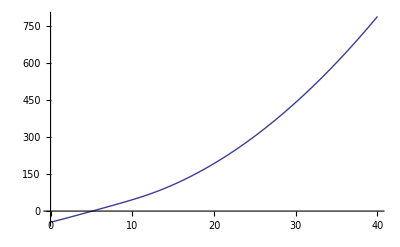

```mathematica
Plot[logL[Z],{Z,0,40}]
```

```mathematica
linspace[x0_,x1_,n_]:=N[Range[x0,x1,(x1-x0)/(n-1)]];
```

```mathematica
Zmax = 50;
x = linspace[0,Zmax,5*Zmax];
y = Map[logL,x];
```

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"logI.dat"}],
Prepend[Transpose[{N[x], y}],{"abs_z","log_I"}],"Table"]
```

/home/javier/work/GW/ligo_template_matching/1-estimate_parameters/logI.dat